# Confronting CPL parameterisation with LCDM using JLA data set

## Created by C. Escamilla-Rivera. March 2017

You are free to use, distribute, and modify this code, as long as you cite the respective papers/references:
(I) Status on bidimensional dark energy parameterizations using SNe Ia JLA and BAO datasets. Galaxies 4 (2016) 8
(II) Linear and non-linear perturbations in dark energy models. JCAP 1611 (2016) no.11, 010

Can I modify the code? 
Yes, you can. In fact, I actively encourage it! It would be great if you could release any modifications that you make to the code, so that they can be shared by everyone. I’m not a stickler about it, though, as long as: (a) you’re nice about it, (b) make good faith attempts to describe and/or share your modifications if asked, and (c) you give proper credit.

But please do email me if you get stuck: cescamilla@mctp.mx

```mathematica
(*Terminate/Restart Mathematica kernel session*)
Quit[];
```

```mathematica
(*Set the Directory to where the data are*)
SetDirectory["/Users/celiaescamilla/Desktop"];
```

```mathematica
(*Setting priors*)
omi=0.295; 
obi=0.044898; 

(*p:priors*)
omp:=omi;
obp:=obi;
```

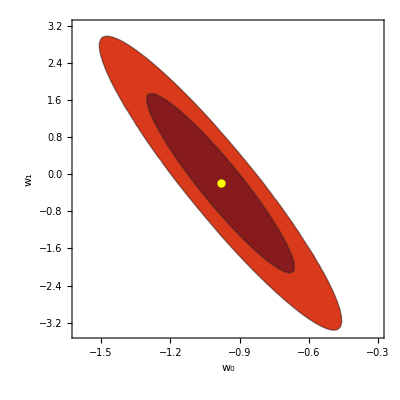

```mathematica
(*Construction of the contour plots via covariance matrix*)
(*Write the  respective files (data reported in columns) with the results included*)
CovSN=Get["covariance_matrix.txt"];
meSN=Get["bestfits.txt"][[2]];
FisSN=Inverse[CovSN];
v[x_,y_]={x,y};
me[i_,j_]:={meSN[[i]],meSN[[j]]};
f[x_,y_,i_,j_]:=(v[x,y]-me[i,j]).FisSN.(v[x,y]-me[i,j]);
SN=FixPolygons[ContourPlot[f[x,y,1,2],{x,-1.6,-0.3},{y,-3.4,3.2},Contours->{2.30,6.17},ContourShading->{{ColorData["SolarColors"][0.007],Opacity[0.9]},{ColorData["SolarColors"][0.27],Opacity[0.9]},Opacity[0.]},FrameLabel->{Subscript[w,0],Subscript[w, 1]}]];
bestSN={{meSN[[1]],meSN[[2]]}};
pbestSN=ListPlot[bestSN,PlotStyle->{Yellow,PointSize[0.015]}];
Show[SN,pbestSN]
```

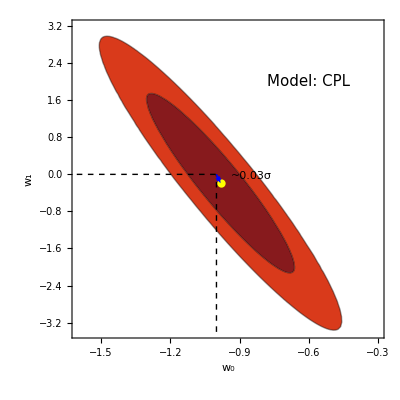

```mathematica
(*Comparison with LCDM model*)
meLCDM={-1,0}; (*Check model first!*)
frS = Graphics[{Arrowheads[{-.03, .03}],Dashed, Blue,Arrow[{{meLCDM[[1]],meLCDM[[2]]}, {meSN[[1]],meSN[[2]]}}]}];
lcdm=Graphics[{Dashing[{0.01,0.01}],Line[{{-1.0,-3.4},{-1.0,0}}],Line[{{-3.,0},{-1.0,0}}]}];
pfrS=Graphics[Text[Style["Model: CPL",FontFamily-> "Helvetica",Italic,FontSize->15],{-0.6,2.}]];
total=Show[SN,pbestSN,lcdm,frS,pfrS,Graphics[Text["~0.03σ",{-0.85,-0.04},TextStyle->{FontFamily->"Times",Blue,FontSize->18}]]]
```

```mathematica
Export["PlotCPL_JLA.pdf",total];
```